### init

```mathematica
basedir="D:\\data\\Cycle 197\\exp_3-16-19\\rawdata\\sc\\"
Get[basedir<>"..\\camera_ifg.m"]
minIntens=2000;  (* Schwellenwert zur Unterdrückung schwach beleuchtetet Randbereiche der Kamera *)
(*
loadimage[basedir<>filename]    liefert Array mit den einzelnen Bildern aus der Tiff-Datei.;
fittile[images_,tileDX_,tileDY_,nx_,ny_,minIntensity_,period_]

*)
```

D:\data\Cycle 197\exp_3-16-19\rawdata\sc\

```mathematica
LoadDatFile[filename_]:=  ToExpression[Transpose[StringSplit[#,"\t"] & /@ Pick[#,StringMatchQ[#,{"\\**","[*"," *","\t*",""}],False]&@Import[basedir<>filename,"lines"]]]
```

```mathematica
reduceSlotsBy[img_,its_,slotmax_]:=Module[{maxph,maxtim},
maxtim=slotmax/its;
maxph=Length[img]/(slotmax+2);
Flatten[Table[    Join[{img[[1+(ph-1)*(slotmax+2)]]},Table[Total[img[[(ph-1)*(slotmax+2)+1+(tim-1)*its;;(ph-1)*(slotmax+2)+tim*its]],1],{tim,1,maxtim}],{img[[ph*(slotmax+2)]]}]     ,{ph,1,maxph}],1]
]
```

```mathematica
(* alle Bilder eines Multi-Page-Images aufsummieren und auf die Anzahl der nicht leeren Pixel normieren *)
integrateImg[img_]:=(Total[#,2]&/@img)   / Count[Flatten[Total[img]],x_/;x>10]
(*integrateImg[img_]:=(Total[#,2]&/@img)   / (Length[img[[1]]]*Length[img[[1,1]]])*)
```

```mathematica
(* counts per pixel *)
cpp[img_]:=N[Total[img,2]  / (Times @@ Dimensions[img])];
```

# Indium 1.0 mm

```mathematica
filename = "ifg1_3p360s_28Jun0049.tif";
```

{31,50,50}

{0.387677,25387.3,9.9732}

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of NonlinearModelFit :: sszero will be suppressed during this calculation.

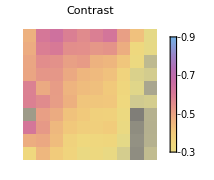
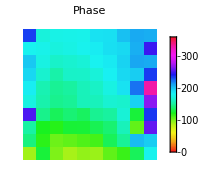
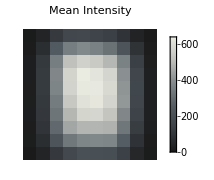
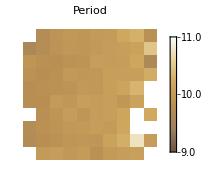

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
totalres=fitarea[img,0,0,Length[img[[1]]], Length[img[[1,1]]] ,1,9][[3;;5]]
res=fitgrid[img,5,5,1.2,+10];
plotres[res]
```

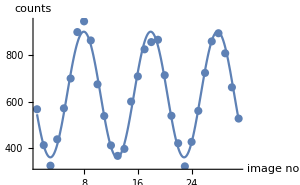
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 630.154 | 4.90274 | 128.531 | 3.57426×10^-39
CameraIfgPackage`Private`b | -269.439 | 7.03095 | -38.3218 | 4.46152×10^-25
CameraIfgPackage`Private`c | 0.631296 | 0.00274368 | 230.091 | 5.38868×10^-46
CameraIfgPackage`Private`d | 2.83032 | 0.0516891 | 54.7566 | 3.28939×10^-29contr=0.427576
offs=630.154
phase=162.165°
period=9.95283

```mathematica
showtileres[res,5,5]
```

```mathematica
filename = "ifg1_3p360s_In_1p0_1_28Jun0724.tif";
```

{31,50,50}

{0.0773403,19393.,6.75972}

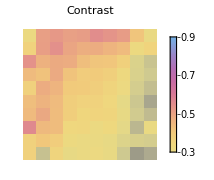
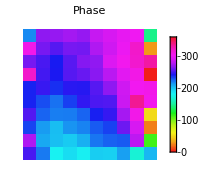
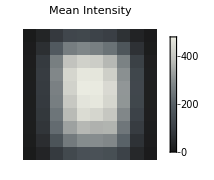
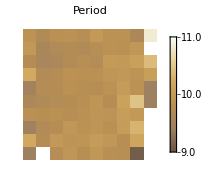

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
totalres=fitarea[img,0,0,Length[img[[1]]], Length[img[[1,1]]] ,1,9][[3;;5]]
res=fitgrid[img,5,5,1.2,+10];
plotres[res]
```

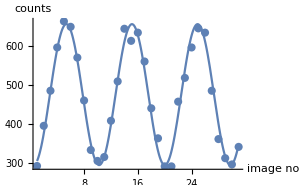
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 475.073 | 4.03306 | 117.795 | 3.7519×10^-38
CameraIfgPackage`Private`b | -180.675 | 5.58819 | -32.3317 | 3.99333×10^-23
CameraIfgPackage`Private`c | 0.643135 | 0.00365925 | 175.756 | 7.72935×10^-43
CameraIfgPackage`Private`d | -1.8736 | 0.0649766 | -28.8349 | 8.07103×10^-22contr=0.380311
offs=475.073
phase=252.651°
period=9.76962

```mathematica
showtileres[res,5,5]
```

```mathematica
filename = "ifg1_3p360s_In_1p0_2_28Jun0406.tif";
```

{31,50,50}

{0.364954,17714.5,9.90858}

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

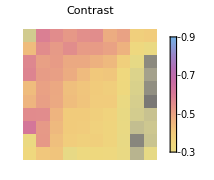
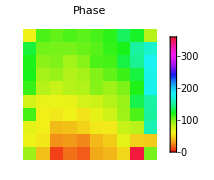
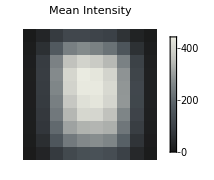
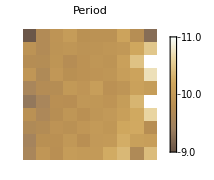

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
totalres=fitarea[img,0,0,Length[img[[1]]], Length[img[[1,1]]] ,1,9][[3;;5]]
res=fitgrid[img,5,5,1.2,+10];
plotres[res]
```

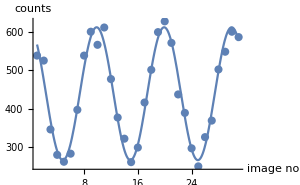
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 438.874 | 4.69954 | 93.3867 | 1.95187×10^-35
CameraIfgPackage`Private`b | -172.613 | 6.53625 | -26.4085 | 8.00795×10^-21
CameraIfgPackage`Private`c | 0.625456 | 0.0042537 | 147.038 | 9.50568×10^-41
CameraIfgPackage`Private`d | 1.68188 | 0.0751988 | 22.3658 | 5.87832×10^-19contr=0.393308
offs=438.874
phase=96.3648°
period=10.0458

```mathematica
showtileres[res,5,5]
```

# Indium 0.5 mm

```mathematica
filename = "ifg1_3p360s_28Jun1930.tif";
```

{31,50,50}

{0.425105,26743.8,9.72801}

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of NonlinearModelFit :: sszero will be suppressed during this calculation.

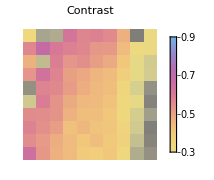
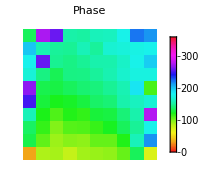
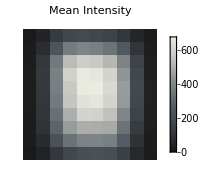
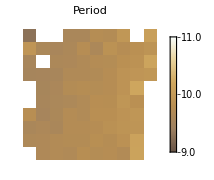

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
totalres=fitarea[img,0,0,Length[img[[1]]], Length[img[[1,1]]] ,1,9][[3;;5]]
res=fitgrid[img,5,5,1.2,+10];
plotres[res]
```

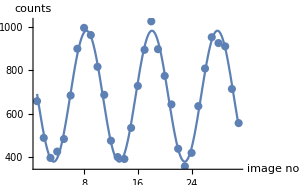
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 679.821 | 5.12283 | 132.704 | 1.51042×10^-39
CameraIfgPackage`Private`b | -301.028 | 7.41329 | -40.6065 | 9.5855×10^-26
CameraIfgPackage`Private`c | 0.644919 | 0.00249884 | 258.087 | 2.43039×10^-47
CameraIfgPackage`Private`d | 2.4622 | 0.0468505 | 52.5544 | 9.86583×10^-29contr=0.442805
offs=679.821
phase=141.074°
period=9.7426

```mathematica
showtileres[res,5,5]
```

```mathematica
filename = "ifg1_3p360s_In_0p5_1_28Jun1613.tif";
```

{31,50,50}

{0.391384,22763.2,10.2699}

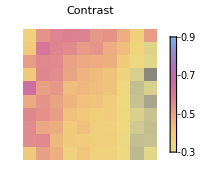
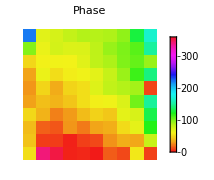
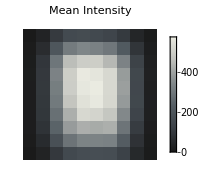
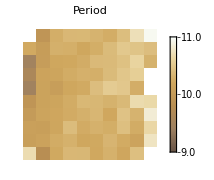

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
totalres=fitarea[img,0,0,Length[img[[1]]], Length[img[[1,1]]] ,1,9][[3;;5]]
res=fitgrid[img,5,5,1.2,+10];
plotres[res]
```

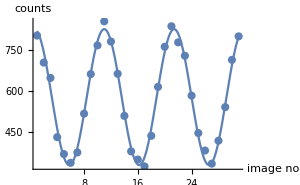
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 576.618 | 4.00039 | 144.141 | 1.6258×10^-40
CameraIfgPackage`Private`b | 248.696 | 5.51292 | 45.1115 | 5.82488×10^-27
CameraIfgPackage`Private`c | 0.604337 | 0.00251136 | 240.642 | 1.60692×10^-46
CameraIfgPackage`Private`d | 1.20637 | 0.0461459 | 26.1426 | 1.04207×10^-20contr=0.431301
offs=576.618
phase=69.1202°
period=10.3968

```mathematica
showtileres[res,5,5]
```

```mathematica
filename = "ifg1_3p360s_In_0p5_2_28Jun2247.tif";
```

{31,50,50}

{0.418602,21925.3,10.0096}

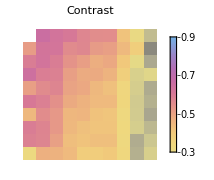
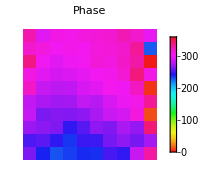
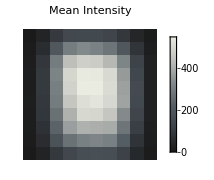
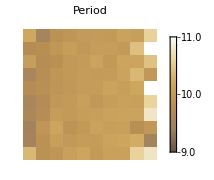

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
totalres=fitarea[img,0,0,Length[img[[1]]], Length[img[[1,1]]] ,1,9][[3;;5]]
res=fitgrid[img,5,5,1.2,+10];
plotres[res]
```

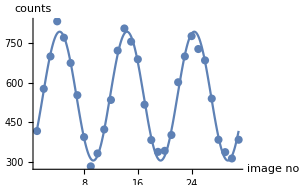
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 549.426 | 4.12458 | 133.208 | 1.36378×10^-39
CameraIfgPackage`Private`b | 244.279 | 5.83856 | 41.8389 | 4.32842×10^-26
CameraIfgPackage`Private`c | 0.627338 | 0.00261048 | 240.315 | 1.66692×10^-46
CameraIfgPackage`Private`d | -1.16803 | 0.0461201 | -25.3259 | 2.37675×10^-20contr=0.444607
offs=549.426
phase=293.077°
period=10.0156

```mathematica
showtileres[res,5,5]
```

# Indium 0.25 mm

```mathematica
filename = "ifg1_3p360s_28Jun0049.tif";
```

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
totalres=fitarea[img,0,0,Length[img[[1]]], Length[img[[1,1]]] ,1,9][[3;;5]]
res=fitgrid[img,5,5,1.2,+10];
plotres[res]
```

{31,50,50}

{0.387677,25387.3,9.9732}

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of NonlinearModelFit :: sszero will be suppressed during this calculation.

-Graphics--Graphics--Graphics--Graphics-

```mathematica
showtileres[res,5,5]
```

-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 630.154 | 4.90274 | 128.531 | 3.57426×10^-39
CameraIfgPackage`Private`b | -269.439 | 7.03095 | -38.3218 | 4.46152×10^-25
CameraIfgPackage`Private`c | 0.631296 | 0.00274368 | 230.091 | 5.38868×10^-46
CameraIfgPackage`Private`d | 2.83032 | 0.0516891 | 54.7566 | 3.28939×10^-29contr=0.427576
offs=630.154
phase=162.165°
period=9.95283

```mathematica
filename = "ifg1_3p360s_In_0p25_1_29Jun1629.tif";
```

{20,50,50}

{0.469468,24007.,10.1891}

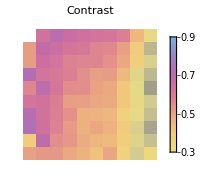
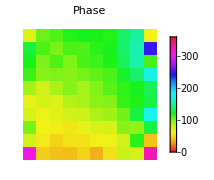
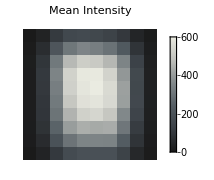
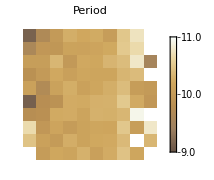

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
totalres=fitarea[img,0,0,Length[img[[1]]], Length[img[[1,1]]] ,1,9][[3;;5]]
res=fitgrid[img,5,5,1.2,+10];
plotres[res]
```

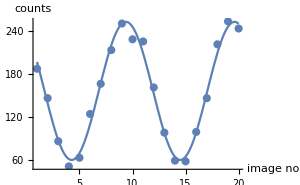
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 156.109 | 2.49221 | 62.6387 | 1.45619×10^-20
CameraIfgPackage`Private`b | -96.153 | 3.3887 | -28.3745 | 4.11738×10^-15
CameraIfgPackage`Private`c | 0.614178 | 0.00614671 | 99.9198 | 8.44071×10^-24
CameraIfgPackage`Private`d | 2.09374 | 0.0683354 | 30.6392 | 1.23073×10^-15contr=0.615935
offs=156.109
phase=119.963°
period=10.2302

```mathematica
showtileres[res,5,9]
```

```mathematica
filename = "ifg1_3p360s_In_1p0_2_28Jun0406.tif";
```

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
totalres=fitarea[img,0,0,Length[img[[1]]], Length[img[[1,1]]] ,1,9][[3;;5]]
res=fitgrid[img,5,5,1.2,+10];
plotres[res]
```

{31,50,50}

{0.364954,17714.5,9.90858}

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

-Graphics--Graphics--Graphics--Graphics-

```mathematica
showtileres[res,5,5]
```

-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 438.874 | 4.69954 | 93.3867 | 1.95187×10^-35
CameraIfgPackage`Private`b | -172.613 | 6.53625 | -26.4085 | 8.00795×10^-21
CameraIfgPackage`Private`c | 0.625456 | 0.0042537 | 147.038 | 9.50568×10^-41
CameraIfgPackage`Private`d | 1.68188 | 0.0751988 | 22.3658 | 5.87832×10^-19contr=0.393308
offs=438.874
phase=96.3648°
period=10.0458